# Blatt 6 - Jonas Neundorf & Jan Skottke

## ANMERKUNGEN!!

Vielleicht guckst du zur Sicherheit nochmal über die Integration für die Verlustleistung. Ich habe da zwar noch jeweils etwas angepasst damit das stimmte, aber ich weiß nicht, ob diese Anpassungen zu 100% richtig sind.
Das Problem beim berechnen des Magnetfeldes konnte ich leider nicht beheben.
Als es um die Zahlenwerte für die Resonatoren ging, war ich mir nicht sicher was ich da genau einsetzten musste. Habe allerdings mal, weil es am meisten Sinn gemacht hat, Werte vom XFEL genommen.
Sonst fällt mir gerade nichts mehr ein. Einfach nochmal drüber gucken, vielleicht findest du ja doch noch irgendeinen Fehler.

## Der “pill-box” Resonator

Aufgrund der Zylindersymmetrie des Resonators bietet es sich an, Zylinderkoordinaten zu benutzen.

### Berechnung des allgemeinen elektrischen Feldes in der TM010 Mode

Lege einige Konstanten fest:

```mathematica
constants = {c -> 3.*10^8, q -> 1.602*10^-19, ϵ -> 1/(Subscript[μ, 0]*c^2), Subscript[μ, 0] -> 4*Pi*10^-7};
```

Lege einen Ansatz fuer das E-Feld an:

```mathematica
e[r,t]:= e[r]*Cos[ω*t];
```

Stelle die Wellengleichung auf:

```mathematica
we=c^2*Laplacian[e[r,t],{r,θ,z},"Cylindrical"] == D[e[r,t],{t,2}]
```

c^2 ((Cos[t ω] e'[r])/r+Cos[t ω] e''[r])==-ω^2 Cos[t ω] e[r]

und löse sie.

```mathematica
solrad=DSolve[{we, e[0]== e0},e[r],r, Assumptions->{r ≤ R, -Infinity < e[r] < Infinity}]//Flatten
```

{e[r]→e0 BesselJ[0,(r ω)/c]}

```mathematica
sol = e[r,t] //. solrad
```

e0 BesselJ[0,(r ω)/c] Cos[t ω]

Nun bestimmen wir die Resonanzfrequenz aus der ersten Nullstelle,

```mathematica
ωres=ω -> c/R BesselJZero[0,1] //. constants;
```

```mathematica
efield ={0,0,1}*e[r]*Cos[ω*t]
```

{0,0,Cos[t ω] e[r]}

### Warum ist es eine “pill box” und keine Bierdose?

Ein ultrarelativistisches Teilchen bewegt sich mit Lichtgeschwindigkeit. Für die Resonatorlänge erhält man also

```mathematica
length=Solve[c == ω/(2*Pi)*2*lResonator, lResonator] //. constants//.ωres //Flatten
```

{lResonator→1.30637 R}

Die Resonatorlänge ist das 1,3-fache des Radius, also kürzer als der Durchmesser der Dose.

### Berechnung des Magnetfeldes

```mathematica
Curl[{hr,hθ,hz}*h[r,t],{r,θ,z},"Cylindrical"]== ϵ*D[efield,{t,1}] //.solrad
```

{0,-hz h^(1,0)[r,t],(hθ h[r,t])/r+hθ h^(1,0)[r,t]}=={0,0,-e0 ϵ ω BesselJ[0,(r ω)/c] Sin[t ω]}

Es folgt: hz =0. Somit können wir die DGL für h(r,t) lösen

```mathematica
dglh= (hθ h[r,t])/r+hθ Derivative[1,0][h][r,t]==-e0*ϵ ω BesselJ[0,(r ω)/c] Sin[t ω]
```

(hθ h[r,t])/r+hθ h^(1,0)[r,t]==-e0 ϵ ω BesselJ[0,(r ω)/c] Sin[t ω]

```mathematica
hfield=DSolve[{dglh,h[0,t]==0},h[r,t],r]//.hθ-> 1 //FullSimplify //Flatten
```

{h[r,t]→-c e0 ϵ BesselJ[1,(r ω)/c] Sin[t ω]}

Das B-Feld zeigt in azimuthale Richtung, seine maximale Stärke ist proportional zu e0*r. Das B-Feld ist also symmetrisch unter Rotationen um die z-Achse.
Begeben wir uns nun auf die Suche nach dem Maximum.

```mathematica
hfdiff = D[hfield, {r, 1}] /. Rule ->Equal /. (l_ == r_) -> r //First
```

-1/2 e0 ϵ ω (BesselJ[0,(r ω)/c]-BesselJ[2,(r ω)/c]) Sin[t ω]

```mathematica
BesselJ[0,(r ω)/c]-BesselJ[2,(r ω)/c]
```

BesselJ[0,(r ω)/c]-BesselJ[2,(r ω)/c]

```mathematica
Solve[{hfdiff ==0 /. t-> Pi/(2*ω)} , r]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{-1/2 e0 ϵ ω (BesselJ[0,(r ω)/c]-BesselJ[2,(r ω)/c])==0},r]

Plottet man die obige Funktion (in willkürlichen Einheiten, da r der einzig freie Parameter ist), so sieht man, dass das B-Feld bei r=0 maximal ist.

### Zahlenbeispiel XFEL

Die Abmessungen des XFEL-Resonators sind (in m):

```mathematica
resonatorRadius = Solve[2*Pi*fres == ω //. ωres //.fres -> 1.3*10^9 //. constants, R] //Flatten
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{R→0.0883246}

```mathematica
resonatorLength = Solve[c == ω/(2*Pi)*2*lResonator, lResonator] //. constants//.ω -> 2*Pi*1.3*10^9 //.resonatorRadius //Flatten
```

{lResonator→0.115385}

### Wie groß ist die im Resonator gespeicherte Feldenergie?

```mathematica
wField = Integrate[ϵ/2*efield.efield*r  //. solrad /.t->0,  {ϕ, 0, 2*Pi}, {z, 0, lResonator }, {r, 0, R }] //FullSimplify //Flatten (*Dimension ist kg*m*s^-2, also Kraft -- du hattest vergessen ein r beim einsetzten des Volumenelements einzufügen*)
```

1/2 e0^2 lResonator π R^2 ϵ (BesselJ[0,(R ω)/c]^2+BesselJ[1,(R ω)/c]^2)

```mathematica
wFieldXFEL = wField //. solrad //. ω -> 2*Pi*1.3*10^9//.resonatorRadius //.e0->25*10^6//. constants //.resonatorLength
```

2.10591

### Berechnung der Ohm’schen Verlustleistung

```mathematica
pDiss = Assuming[{ω>0, c>0, R>0},Subscript[R, s]/2* Integrate[h[r, t]*h[r, t]*r //.hfield //. r-> R, {ϕ, 0, 2*Pi},{z,0,lResonator}] + Subscript[R, s]*Integrate[h[r, t]*h[r, t]*r //.hfield , {r, 0, R},{ϕ,0,2*Pi}]//.t-> Pi/(2*ω)//FullSimplify]
```

(c^2 e0^2 π R ϵ^2 (R ω BesselJ[0,(R ω)/c]^2-2 c BesselJ[0,(R ω)/c] BesselJ[1,(R ω)/c]+(lResonator+R) ω BesselJ[1,(R ω)/c]^2) R_s)/ω

Güte des Resonators

```mathematica
guete = ω* wField/pDiss //FullSimplify
```

(lResonator R ω^2 (BesselJ[0,(R ω)/c]^2+BesselJ[1,(R ω)/c]^2))/(2 c^2 ϵ (R ω BesselJ[0,(R ω)/c]^2-2 c BesselJ[0,(R ω)/c] BesselJ[1,(R ω)/c]+(lResonator+R) ω BesselJ[1,(R ω)/c]^2) R_s)

Alle Einheiten passen jetzt bis hier hin!!!!!!  Damit ist der Geometriefaktor, alles was vor 1/ R_s steht!

### Zahlenwerte für normal- und supraleitende Resonatoren

Zuerst die Werte für normalleitende Resonatoren

```mathematica
Rsn= Subscript[R, s]-> 1/(σ*δ)
```

R_s→1/(δ σ)

```mathematica
delta= δ-> √(2/(Subscript[μ, 0]*ω*σ))
```

δ→√2 √(1/(σ ω μ_0))

δ→√2 √(1/(σ ω μ_0))

Die Güte ist

```mathematica
guete//.Rsn//.delta//. σ-> 7.*10^7//.length //.resonatorRadius//.constants//.ω -> 2*Pi*1.3*10^9 (*werte für xfel eingesetzt*)
```

29986.1

Die Verlustleistung ist

```mathematica
pDiss//.Rsn//.delta//. σ-> 7.*10^7//.length //.resonatorRadius//.constants//.ω -> 2*Pi*1.3*10^9 //.e0-> 25.*10^6
```

573646.

Nun die Werte für den supraleitenden Resonator

```mathematica
Rss= Subscript[R, s]->9*10^-5*f^2/T*Exp[-1.85*Tc/T]
```

R_s→(9 ⅇ^(-(1.85 Tc)/T) f^2)/(100000 T)

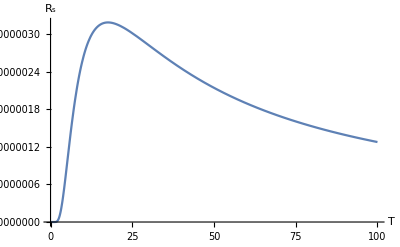

```mathematica
Plot[9*10^-5*f^2/T*Exp[-1.85*Tc/T]//.f-> 1.3//. Tc-> 9.5,{T,0,100}, AxesLabel->{T,Subscript[R, s]}]
```

Berechne nun die Verlustleistung für T=4.2K

```mathematica
pDiss//.Rss//.delta//. σ-> 7.*10^7//.length //.resonatorRadius//.constants//.ω -> 2*Pi*1.3*10^9 //.e0-> 25.*10^6//. f-> 1.3//. Tc-> 9.5//. T-> 4.2
```

36.9493

und für T=2K

```mathematica
pDiss//.Rss//.delta//. σ-> 7.*10^7//.length //.resonatorRadius//.constants//.ω -> 2*Pi*1.3*10^9 //.e0-> 25.*10^6//. f-> 1.3//. Tc-> 9.5//. T-> 2
```

0.777639

Die Verlustleistungen für supraleitende Resonatoren sind um ein Vielfaches niediger als die für Kupfer.